# IBM Rxn Evaluation Write-up Figures

## Import Data

```mathematica
dat=SemanticImport["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\retro\\allDatAnaly98.csv"];
```

## IBM Rxn API Wrapper Code - (https://github.com/wrborrelli/IBMRxnAPI)

### Necessary Variable Assignments

```mathematica
(* Initial run of this notebook will prompt you to enter your authorization key. Once you've done that feel free to delete the following cell. *)
```

```mathematica
(*SystemCredential["authKey"]=InputString["Authorization Key"];*)
```

```mathematica
authKey=SystemCredential["authKey"];
```

### Wrapper Code

```mathematica
baseURL="rxn.res.ibm.com";
```

```mathematica
IBMRxn[req_String,molecs_List,projID_String]:=Module[
{reactantList={},createProj,projectID,createPred,getPred,rxnImg,rxnConf,predID,projName,reactants},

If[(* If[] you want to make a "new prediction", this code block runs *)
req=="new prediction",
Do[
Which[
ImageQ[molecs[[i]]],
AppendTo[reactantList,MoleculeRecognize[molecs[[i]]]["SMILES"]]
,
StringQ[molecs[[i]]],
AppendTo[reactantList,molecs[[i]]]
],{i,1,Length[molecs]}];

reactants=ToString[Row[#,"."]&@reactantList];
createPred=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/predictions/pr?projectId="<>projID],
<|"Method"->"POST",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>,
"Body"->ExportString[<|"reactants"->reactants|>,"JSON"]|>]//URLExecute[#,"RawJSON"]&;
predID=createPred["payload","id"];

Pause[10];

getPred=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/predictions/"<>predID],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;

projName=StringReplace[getPred["payload","attempts"][[1]]["name"],"_"~~___->""];
projectID=getPred["payload","attempts"][[1]]["projectId"];
rxnImg=ResourceFunction["SVGImport"][getPred["payload","attempts"][[1]]["reactionImage"]];
rxnConf=getPred["payload","attempts"][[1]]["confidence"];

rxnImg
TableForm[{{projName,projectID,predID,rxnConf}},TableHeadings->{None,{"Project Name","Project ID","Prediction ID","Prediction Confidence"}}]
]]
```

```mathematica
(* duplicate of above - for adding a output format parameter *)
```

```mathematica
IBMRxn[req_String,molecs_List,projID_String,outType_String]:=Module[
{reactantList={},createProj,projectID,createPred,getPred,rxnImg,rxnConf,predID,projName,reactants,rsmiles},

If[(* If[] you want to make a "new prediction", this code block runs *)
req=="new prediction",
Do[
Which[
ImageQ[molecs[[i]]],
AppendTo[reactantList,MoleculeRecognize[molecs[[i]]]["SMILES"]]
,
StringQ[molecs[[i]]],
AppendTo[reactantList,molecs[[i]]]
],{i,1,Length[molecs]}];

reactants=ToString[Row[#,"."]&@reactantList];
createPred=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/predictions/pr?projectId="<>projID],
<|"Method"->"POST",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>,
"Body"->ExportString[<|"reactants"->reactants|>,"JSON"]|>]//URLExecute[#,"RawJSON"]&;
predID=createPred["payload","id"];

Pause[10];

getPred=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/predictions/"<>predID],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;

Which[
outType==""||StringMatchQ[ToString@outType,"default",IgnoreCase->True],
projName=StringReplace[getPred["payload","attempts"][[1]]["name"],"_"~~___->""];
projectID=getPred["payload","attempts"][[1]]["projectId"];
rxnImg=ResourceFunction["SVGImport"][getPred["payload","attempts"][[1]]["reactionImage"]];
rxnConf=getPred["payload","attempts"][[1]]["confidence"];

rxnImg
TableForm[{{projName,projectID,predID,rxnConf}},TableHeadings->{None,{"Project Name","Project ID","Prediction ID","Prediction Confidence"}}]
,
StringMatchQ[ToString@outType,"dataset",IgnoreCase->True],
projName=StringReplace[getPred["payload","attempts"][[1]]["name"],"_"~~___->""];
projectID=getPred["payload","attempts"][[1]]["projectId"];
rxnImg=ResourceFunction["SVGImport"][getPred["payload","attempts"][[1]]["reactionImage"]];
rxnConf=getPred["payload","attempts"][[1]]["confidence"];
rsmiles=getPred["payload","attempts"][[1]]["smiles"];

<|"project name"->projName,"projID"->projectID,"predID"->predID,"rreac"->reacSplit[rsmiles][[1]],"rprod"->reacSplit[rsmiles][[2]],"conf"->rxnConf,"reaction image"->rxnImg|>//Dataset
]
]]
```

```mathematica
(* for getting more outcomes from a prediction that you've already made *)
```

```mathematica
IBMRxn[req_String,projID_String,predID_String]:=Module[
{getPred,reactants,morePreds,projName,rxnImgList={},rxnConfList={},rxnImages,rxnTables,preds},

If[req=="more predictions",
getPred=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/predictions/"<>predID],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>
|>]//URLExecute[#,"RawJSON"]&;
reactants=getPred["payload","request","reactants"];

Pause[10];

morePreds=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/predictions/prb?predictionId="<>predID<>"&projectId="<>projID],
<|"Method"->"POST",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>,
"Body"->ExportString[<|"reactants"->reactants|>,"JSON"]|>]//URLExecute[#,"RawJSON"]&;

Pause[10];

getPred=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/predictions/"<>predID],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;

projName=StringReplace[getPred["payload","attempts"][[1]]["name"],"_"~~___->""];

Do[(* add each rxn img to the list *)
AppendTo[rxnImgList,getPred["payload","attempts"][[i]]["reactionImage"]],
{i,1,Length[getPred["payload","attempts"]]}];
Do[(* add each confidence to the list *)
AppendTo[rxnConfList,getPred["payload","attempts"][[i]]["confidence"]],
{i,1,Length[getPred["payload","attempts"]]}];


rxnImages=ResourceFunction["SVGImport"][#]&/@rxnImgList;
rxnTables=TableForm[{{projName,projID,predID,#}},TableHeadings->{None,{"Project Name","Project ID","Prediction ID","Prediction Confidence"}}]&/@rxnConfList;

preds=Partition[Riffle[rxnImages,rxnTables],2];
preds
]]
```

```mathematica
(* duplicate of above - for adding an output type *)
```

```mathematica
IBMRxn[req_String,projID_String,predID_String,outType_String]:=Module[
{getPred,reactants,morePreds,projName,rxnImgList={},rxnConfList={},rsmilesList={},rxnImages,rxnTables,preds},

If[req=="more predictions",
getPred=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/predictions/"<>predID],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>
|>]//URLExecute[#,"RawJSON"]&;
reactants=getPred["payload","request","reactants"];

Pause[10];

morePreds=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/predictions/prb?predictionId="<>predID<>"&projectId="<>projID],
<|"Method"->"POST",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>,
"Body"->ExportString[<|"reactants"->reactants|>,"JSON"]|>]//URLExecute[#,"RawJSON"]&;

Pause[10];

getPred=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/predictions/"<>predID],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;

Which[
outType==""||StringMatchQ[ToString@outType,"default",IgnoreCase->True],
projName=StringReplace[getPred["payload","attempts"][[1]]["name"],"_"~~___->""];

Do[(* add each rxn img to the list *)
AppendTo[rxnImgList,getPred["payload","attempts"][[i]]["reactionImage"]],
{i,1,Length[getPred["payload","attempts"]]}];
Do[(* add each confidence to the list *)
AppendTo[rxnConfList,getPred["payload","attempts"][[i]]["confidence"]],
{i,1,Length[getPred["payload","attempts"]]}];


rxnImages=ResourceFunction["SVGImport"][#]&/@rxnImgList;
rxnTables=TableForm[{{projName,projID,predID,#}},TableHeadings->{None,{"Project Name","Project ID","Prediction ID","Prediction Confidence"}}]&/@rxnConfList;

preds=Partition[Riffle[rxnImages,rxnTables],2];
preds
,
StringMatchQ[ToString@outType,"dataset",IgnoreCase->True],
projName=StringReplace[getPred["payload","attempts"][[1]]["name"],"_"~~___->""];

Do[(* add each rxn img to the list *)
AppendTo[rxnImgList,getPred["payload","attempts"][[i]]["reactionImage"]],
{i,1,Length[getPred["payload","attempts"]]}];
	Do[(* add each confidence to the list *)
AppendTo[rxnConfList,getPred["payload","attempts"][[i]]["confidence"]],
{i,1,Length[getPred["payload","attempts"]]}];
Do[(* add each rsmiles to the list *)
AppendTo[rsmilesList,getPred["payload","attempts"][[i]]["smiles"]],
{i,1,Length[getPred["payload","attempts"]]}];

rxnImages=ResourceFunction["SVGImport"][#]&/@rxnImgList;

Dataset@MapThread[<|"project name"->projName,"projID"->projID,"predID"->predID,"rreac"->reacSplit[#1][[1]],"rprod"->reacSplit[#1][[2]],"conf"->#2,"reaction image"->#3|>&,{rsmilesList,rxnConfList,rxnImages}]
]
]]
```

```mathematica
(* for making a new retrosynthesis *)
```

```mathematica
IBMRxn[req_String,projID_String,prod_List]:=Module[
{prodSMILE,createRet,retID,getRet,seqMolecList,seqSMILES,molecPlots,stepsImgs,stepDescs,retTable,retConf,retOptScore,retImg,rClass,seqConf,arrow=Graphics[Text@Style["⇒",60],BaselinePosition->Center,ImageSize->100]},

If[(* this code block runs to make and get a new retrosynthesis *)
req=="new retrosynthesis",
Which[
ImageQ[prod[[1]]],
prodSMILE=MoleculeRecognize[prod[[1]]]["SMILES"],
StringQ[prod[[1]]],
prodSMILE=prod[[1]]
];

createRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/rs?projectId="<>projID],
<|"Method"->"POST",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>,
"Body"->ExportString[<|
"isInteractive"->"false",
"parameters"-><|"availability_pricing_threshold"->0,
"available_smiles"->"",
"exclude_smiles"->"",
"exclude_substructures"->"",
"exclude_target_molecule"->"true",
"fap"->0,
"max_steps"->0,
"nbeams"->0,
"pruning_steps"->0|>,
"product"->prodSMILE
|>,"JSON"]|>]//URLExecute[#,"RawJSON"]&;
retID=createRet["payload","id"];

Pause[10];

getRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/"<>retID],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;
While[(* Loops until the get request says the task status is "DONE" *)
getRet["payload","task","status"]≠"DONE",
Pause[10];
getRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/"<>retID],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;

];
retConf=getRet["payload","sequences"][[1]]["confidence"];
seqConf=getRet["payload","siblings"][[-1]]["reactions"][[1]]["confidence"];
retOptScore=getRet["payload","sequences"][[1]]["optimizationScore"];

molecPlots=MoleculePlot[Molecule[StringReplace[getRet["payload","siblings"][[-1]]["reactions"][[1]]["smiles"],"~"->"."]],ImageSize->Large];
retImg=GraphicsRow[{MoleculePlot[Molecule[prodSMILE]],arrow,StringReplace[getRet["payload","siblings"][[-1]]["reactions"][[1]]["smiles"],"~"->"."]//Molecule//MoleculePlot}];
rClass=getRet["payload","siblings"][[-1]]["reactions"][[1]]["rclass"];
retTable=TableForm[{{projID,retID,retConf,retOptScore,rClass,seqConf}},TableHeadings->{None,{"Project ID","Retrosynthesis ID","Retrosynthesis Confidence","Retrosynthesis Optimization Score","Reaction Class","Sequence Confidence"}}];

retImg
retTable
]]
```

```mathematica
(* duplicate of above - added to specify a precursor *)
```

```mathematica
IBMRxn[req_String,projID_String,prod_List,prec_String]:=Module[
{prodSMILE,createRet,retID,getRet,seqMolecList,seqSMILES,molecPlots,stepsImgs,stepDescs,retTable,retConf,retOptScore,retImg,rClass,seqConf,arrow=Graphics[Text@Style["⇒",60],BaselinePosition->Center,ImageSize->100],out,seqs,childsNumb,cImgs,childs,product},

If[(* this code block runs to make and get a new retrosynthesis *)
req=="new retrosynthesis",
Which[
ImageQ[prod[[1]]],
prodSMILE=MoleculeRecognize[prod[[1]]]["SMILES"],
StringQ[prod[[1]]],
prodSMILE=prod[[1]]
];

createRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/rs?projectId="<>projID],
<|"Method"->"POST",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>,
"Body"->ExportString[<|
"isInteractive"->"false",
"parameters"-><|"availability_pricing_threshold"->0,
"available_smiles"->prec,
"exclude_smiles"->"",
"exclude_substructures"->"",
"exclude_target_molecule"->"true",
"fap"->0,
"max_steps"->0,
"nbeams"->0,
"pruning_steps"->0|>,
"product"->prodSMILE
|>,"JSON"]|>]//URLExecute[#,"RawJSON"]&;
retID=createRet["payload","id"];

Pause[10];

getRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/"<>retID],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;
While[(* Loops until the get request says the task status is "DONE" *)
getRet["payload","task","status"]≠"DONE",
Pause[10];
getRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/"<>retID],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;

];
(*retConf=getRet["payload","sequences"][[1]]["confidence"];
seqConf=getRet["payload","siblings"][[-1]]["reactions"][[1]]["confidence"];
retOptScore=getRet["payload","sequences"][[1]]["optimizationScore"];

molecPlots=MoleculePlot[Molecule[StringReplace[getRet["payload","siblings"][[-1]]["reactions"][[1]]["smiles"],"~"->"."]],ImageSize->Large];
retImg=GraphicsRow[{MoleculePlot[Molecule[prodSMILE]],arrow,StringReplace[getRet["payload","siblings"][[-1]]["reactions"][[1]]["smiles"],"~"->"."]//Molecule//MoleculePlot}];
rClass=getRet["payload","siblings"][[-1]]["reactions"][[1]]["rclass"];*)

seqs=Length@getRet["payload","sequences"];

retImg=Table[
product=getRet["payload","sequences"][[i]]["tree","smiles"]//Molecule//MoleculePlot;
rClass=getRet["payload","sequences"][[i]]["tree","rclass"];
retOptScore=getRet["payload","sequences"][[i]]["optimizationScore"];
retConf=getRet["payload","sequences"][[i]]["confidence"];
childsNumb=getRet["payload","sequences"][[i]]["tree","children"]//Length;
out=Reap[Do[
childs=getRet["payload","sequences"][[i]]["tree","children"][[n]]["smiles"];
Sow[childs];
,{n,1,childsNumb}]];
cImgs=Map[MoleculePlot[#]&,Molecule[#]&/@Flatten@Rest@out];

retImg=GraphicsRow[{product,arrow,cImgs},ImageSize->Full];
retTable=TableForm[{{projID,retID,retConf,retOptScore,rClass}},TableHeadings->{None,{"Project ID","Retrosynthesis ID","Retrosynthesis Confidence","Retrosynthesis Optimization Score","Reaction Class"}}];

Column[{retImg,retTable}]
,{i,1,seqs}]

(*retTable=TableForm[{{projID,retID,retConf,retOptScore,rClass,seqConf}},TableHeadings->{None,{"Project ID","Retrosynthesis ID","Retrosynthesis Confidence","Retrosynthesis Optimization Score","Reaction Class","Sequence Confidence"}}];*)
]]
```

```mathematica
(* duplicate of above - added to specify output type *)
```

```mathematica
IBMRxn[req_String,projID_String,prod_List,prec_String,outType_String]:=Module[
{prodSMILE,createRet,retID,getRet,seqMolecList,seqSMILES,molecPlots,stepsImgs,stepDescs,retTable,retConf,retOptScore,retImg,rClass,seqConf,arrow=Graphics[Text@Style["⇒",60],BaselinePosition->Center,ImageSize->100],out,seqs,childsNumb,cImgs,childs,product,cols,cSMILES,retroID},

If[(* this code block runs to make and get a new retrosynthesis *)
req=="new retrosynthesis",
Which[
ImageQ[prod[[1]]],
prodSMILE=MoleculeRecognize[prod[[1]]]["SMILES"],
StringQ[prod[[1]]],
prodSMILE=prod[[1]]
];

createRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/rs?projectId="<>projID],
<|"Method"->"POST",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>,
"Body"->ExportString[<|
"isInteractive"->"false",
"parameters"-><|"availability_pricing_threshold"->0,
"available_smiles"->prec,
"exclude_smiles"->"",
"exclude_substructures"->"",
"exclude_target_molecule"->"true",
"fap"->0,
"max_steps"->0,
"nbeams"->0,
"pruning_steps"->0|>,
"product"->prodSMILE
|>,"JSON"]|>]//URLExecute[#,"RawJSON"]&;
retID=createRet["payload","id"];

Pause[10];

getRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/"<>retID],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;
While[(* Loops until the get request says the task status is "DONE" *)
getRet["payload","task","status"]≠"DONE",
Pause[10];
getRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/"<>retID],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;

];
(*retConf=getRet["payload","sequences"][[1]]["confidence"];
seqConf=getRet["payload","siblings"][[-1]]["reactions"][[1]]["confidence"];
retOptScore=getRet["payload","sequences"][[1]]["optimizationScore"];

molecPlots=MoleculePlot[Molecule[StringReplace[getRet["payload","siblings"][[-1]]["reactions"][[1]]["smiles"],"~"->"."]],ImageSize->Large];
retImg=GraphicsRow[{MoleculePlot[Molecule[prodSMILE]],arrow,StringReplace[getRet["payload","siblings"][[-1]]["reactions"][[1]]["smiles"],"~"->"."]//Molecule//MoleculePlot}];
rClass=getRet["payload","siblings"][[-1]]["reactions"][[1]]["rclass"];*)

Which[outType==""||StringMatchQ[ToString@outType,"default",IgnoreCase->True],
seqs=Length@getRet["payload","sequences"];

retImg=Table[
product=getRet["payload","sequences"][[i]]["tree","smiles"]//Molecule//MoleculePlot;
rClass=getRet["payload","sequences"][[i]]["tree","rclass"];
retOptScore=getRet["payload","sequences"][[i]]["optimizationScore"];
retConf=getRet["payload","sequences"][[i]]["confidence"];
childsNumb=getRet["payload","sequences"][[i]]["tree","children"]//Length;
out=Reap[Do[
childs=getRet["payload","sequences"][[i]]["tree","children"][[n]]["smiles"];
Sow[childs];
,{n,1,childsNumb}]];
cImgs=Map[MoleculePlot[#]&,Molecule[#]&/@Flatten@Rest@out];

retImg=GraphicsRow[{product,arrow,cImgs},ImageSize->Full];
retTable=TableForm[{{projID,retID,retConf,retOptScore,rClass}},TableHeadings->{None,{"Project ID","Retrosynthesis ID","Retrosynthesis Confidence","Retrosynthesis Optimization Score","Reaction Class"}}];

Column[{retImg,retTable}]
,{i,1,seqs}]
,
StringMatchQ[ToString@outType,"dataset",IgnoreCase->True],
seqs=Length@getRet["payload","sequences"];

cols=Table[
product=getRet["payload","sequences"][[i]]["tree","smiles"];
retroID=getRet["payload","sequences"][[1]]["retrosynthesisId"];
rClass=getRet["payload","sequences"][[i]]["tree","rclass"];
retOptScore=getRet["payload","sequences"][[i]]["optimizationScore"];
retConf=getRet["payload","sequences"][[i]]["confidence"];
childsNumb=getRet["payload","sequences"][[i]]["tree","children"]//Length;
out=Reap[Do[
childs=getRet["payload","sequences"][[i]]["tree","children"][[n]]["smiles"];
Sow[childs];
,{n,1,childsNumb}]];
cSMILES=Flatten@Rest@out;

{rClass,projID,retroID,cSMILES,product,retConf,retOptScore}
,{i,1,seqs}];
MapThread[<|"rclass"->#1,"projID"->#2,"retroID"->#3,"rreac"->StringRiffle[#4,"."],"prod"->#5,"conf"->#6,"opt"->#7|>&,{cols[[All,1]],cols[[All,2]],cols[[All,3]],cols[[All,4]],cols[[All,5]],cols[[All,6]],cols[[All,7]]}]//Dataset
]

(*retTable=TableForm[{{projID,retID,retConf,retOptScore,rClass,seqConf}},TableHeadings->{None,{"Project ID","Retrosynthesis ID","Retrosynthesis Confidence","Retrosynthesis Optimization Score","Reaction Class","Sequence Confidence"}}];*)
]]
```

```mathematica
(* for making a new project, listing all project attempts, or recovering a past prediction or retrosynthesis *)
```

```mathematica
IBMRxn[req_String,IDorName_String]:=Module[
{myProjects,myProjNames,myProjIDs,nameRule,idRule,myProjectsData,allProjAs,getPred,projName,rxnImg,rxnConf,predID,projID,createProj,projectID,getRet,seqMolecList,seqSMILES,retConf,retOptScore,molecPlots,retTable,stepsImgs,arrow=Graphics[Text@Style["⇒",60],BaselinePosition->Center,ImageSize->100],stepDescs,retImg,prodSMILES,rClass,seqConf,seqs,prod,childsNumb,out,cImgs,childs},

Which[
req=="new project",(* for a "new project", following code block runs *)
createProj=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/projects"],
<|"Method"->"POST",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>,
"Body"->ExportString[<|"name"->ToString[IDorName],"invitations"->{}|>,"JSON"]|>]//URLExecute[#,"RawJSON"]&;
projectID=createProj["payload","id"];
TableForm[{{IDorName,projectID}},TableHeadings->{None,{"Project Name","Project ID"}}]
,
req== "all project attempts",(* for getting "all project attempts", following code block runs *)
allProjAs=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/projects/"<>IDorName<>"/attempts?raw={}"],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>
|>]//URLExecute[#,"RawJSON"]&;
allProjAs,
req=="recover prediction",(* to "recover prediction", following code block runs *)
getPred=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/predictions/"<>IDorName],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;
projName=StringReplace[getPred["payload","attempts"][[1]]["name"],"_"~~___->""];
projID=getPred["payload","attempts"][[1]]["projectId"];
predID=getPred["payload","id"];
rxnImg=ResourceFunction["SVGImport"][getPred["payload","attempts"][[1]]["reactionImage"]];
rxnConf=getPred["payload","attempts"][[1]]["confidence"];

rxnImg
TableForm[{{projName,projID,predID,rxnConf}},TableHeadings->{None,{"Project Name","Project ID","Prediction ID","Prediction Confidence"}}]
,
req=="recover retrosynthesis",(* recover a previously made retrosynthesis *)
getRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/"<>IDorName],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;

While[
getRet["payload","task","status"]≠"DONE",
Pause[10];
getRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/"<>IDorName],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;

];
projID=getRet["payload","projectId"];

(*retConf=getRet["payload","sequences"][[1]]["confidence"];
seqConf=getRet["payload","siblings"][[-1]]["reactions"][[1]]["confidence"];
retOptScore=getRet["payload","sequences"][[1]]["optimizationScore"];

prodSMILES=getRet["payload","wizardParameters","exclude_smiles"][[1]];
molecPlots=MoleculePlot[Molecule[StringReplace[getRet["payload","siblings"][[-1]]["reactions"][[1]]["smiles"],"~"->"."]],ImageSize->Large];
rClass=getRet["payload","siblings"][[-1]]["reactions"][[1]]["rclass"];

retImg=GraphicsRow[{MoleculePlot[Molecule[prodSMILES]],arrow,StringReplace[getRet["payload","siblings"][[-1]]["reactions"][[1]]["smiles"],"~"->"."]//Molecule//MoleculePlot}];*)

seqs=Length@getRet["payload","sequences"];

retImg=Table[
prod=getRet["payload","sequences"][[i]]["tree","smiles"]//Molecule//MoleculePlot;
rClass=getRet["payload","sequences"][[i]]["tree","rclass"];
retOptScore=getRet["payload","sequences"][[i]]["optimizationScore"];
retConf=getRet["payload","sequences"][[i]]["confidence"];
childsNumb=getRet["payload","sequences"][[i]]["tree","children"]//Length;
out=Reap[Do[
childs=getRet["payload","sequences"][[i]]["tree","children"][[n]]["smiles"];
Sow[childs];
,{n,1,childsNumb}]];
cImgs=Map[MoleculePlot[#]&,Molecule[#]&/@Flatten@Rest@out];

retImg=GraphicsRow[{prod,arrow,cImgs},ImageSize->Full];
retTable=TableForm[{{projID,IDorName,retConf,retOptScore,rClass}},TableHeadings->{None,{"Project ID","Retrosynthesis ID","Retrosynthesis Confidence","Retrosynthesis Optimization Score","Reaction Class"}}];

Column[{retImg,retTable}]
,{i,1,seqs}]

(*retImg=GraphicsRow[{MoleculePlot[Molecule[prodSMILES]],arrow,StringReplace[getRet["payload","siblings"][[-1]]["reactions"][[1]]["smiles"],"~"->"."]//Molecule//MoleculePlot}];*)
]]
```

```mathematica
(* duplicate of above - added to allow for specifying ouput type *)
```

```mathematica
IBMRxn[req_String,IDorName_String,outType_String]:=Module[
{myProjects,myProjNames,myProjIDs,nameRule,idRule,myProjectsData,allProjAs,getPred,projName,rxnImg,rxnConf,predID,projID,createProj,projectID,getRet,seqMolecList,seqSMILES,retConf,retOptScore,molecPlots,retTable,stepsImgs,arrow=Graphics[Text@Style["⇒",60],BaselinePosition->Center,ImageSize->100],stepDescs,retImg,prodSMILES,rClass,seqConf,seqs,prod,childsNumb,out,cImgs,childs,retroID,product,cols,cSMILES,rsmiles},

Which[
req=="new project",(* for a "new project", following code block runs *)
createProj=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/projects"],
<|"Method"->"POST",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>,
"Body"->ExportString[<|"name"->ToString[IDorName],"invitations"->{}|>,"JSON"]|>]//URLExecute[#,"RawJSON"]&;
projectID=createProj["payload","id"];
TableForm[{{IDorName,projectID}},TableHeadings->{None,{"Project Name","Project ID"}}]
,
req== "all project attempts",(* for getting "all project attempts", following code block runs *)
allProjAs=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/projects/"<>IDorName<>"/attempts?raw={}"],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>
|>]//URLExecute[#,"RawJSON"]&;
allProjAs,
req=="recover prediction",(* to "recover prediction", following code block runs *)
getPred=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/predictions/"<>IDorName],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;
Which[outType==""||StringMatchQ[ToString@outType,"default",IgnoreCase->True],
projName=StringReplace[getPred["payload","attempts"][[1]]["name"],"_"~~___->""];
projID=getPred["payload","attempts"][[1]]["projectId"];
predID=getPred["payload","id"];
rxnImg=ResourceFunction["SVGImport"][getPred["payload","attempts"][[1]]["reactionImage"]];
rxnConf=getPred["payload","attempts"][[1]]["confidence"];

rxnImg
TableForm[{{projName,projID,predID,rxnConf}},TableHeadings->{None,{"Project Name","Project ID","Prediction ID","Prediction Confidence"}}]
,
StringMatchQ[ToString@outType,"dataset",IgnoreCase->True],
projName=StringReplace[getPred["payload","attempts"][[1]]["name"],"_"~~___->""];
projID=getPred["payload","attempts"][[1]]["projectId"];
predID=getPred["payload","id"];
rxnImg=ResourceFunction["SVGImport"][getPred["payload","attempts"][[1]]["reactionImage"]];
rxnConf=getPred["payload","attempts"][[1]]["confidence"];
rsmiles=getPred["payload","attempts"][[1]]["smiles"];

<|"project name"->projName,"projID"->projID,"predID"->predID,"rreac"->reacSplit[rsmiles][[1]],"rprod"->reacSplit[rsmiles][[2]],"conf"->rxnConf,"reaction image"->rxnImg|>//Dataset
]
,
req=="recover retrosynthesis",(* recover a previously made retrosynthesis *)
getRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/"<>IDorName],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;

While[
getRet["payload","task","status"]≠"DONE",
Pause[10];
getRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/"<>IDorName],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;

];
projID=getRet["payload","projectId"];

(*retConf=getRet["payload","sequences"][[1]]["confidence"];
seqConf=getRet["payload","siblings"][[-1]]["reactions"][[1]]["confidence"];
retOptScore=getRet["payload","sequences"][[1]]["optimizationScore"];

prodSMILES=getRet["payload","wizardParameters","exclude_smiles"][[1]];
molecPlots=MoleculePlot[Molecule[StringReplace[getRet["payload","siblings"][[-1]]["reactions"][[1]]["smiles"],"~"->"."]],ImageSize->Large];
rClass=getRet["payload","siblings"][[-1]]["reactions"][[1]]["rclass"];

retImg=GraphicsRow[{MoleculePlot[Molecule[prodSMILES]],arrow,StringReplace[getRet["payload","siblings"][[-1]]["reactions"][[1]]["smiles"],"~"->"."]//Molecule//MoleculePlot}];*)

Which[outType==""||StringMatchQ[ToString@outType,"default",IgnoreCase->True],
seqs=Length@getRet["payload","sequences"];

retImg=Table[
prod=getRet["payload","sequences"][[i]]["tree","smiles"]//Molecule//MoleculePlot;
rClass=getRet["payload","sequences"][[i]]["tree","rclass"];
retOptScore=getRet["payload","sequences"][[i]]["optimizationScore"];
retConf=getRet["payload","sequences"][[i]]["confidence"];
childsNumb=getRet["payload","sequences"][[i]]["tree","children"]//Length;
out=Reap[Do[
childs=getRet["payload","sequences"][[i]]["tree","children"][[n]]["smiles"];
Sow[childs];
,{n,1,childsNumb}]];
cImgs=Map[MoleculePlot[#]&,Molecule[#]&/@Flatten@Rest@out];

retImg=GraphicsRow[{prod,arrow,cImgs},ImageSize->Full];
retTable=TableForm[{{projID,IDorName,retConf,retOptScore,rClass}},TableHeadings->{None,{"Project ID","Retrosynthesis ID","Retrosynthesis Confidence","Retrosynthesis Optimization Score","Reaction Class"}}];

Column[{retImg,retTable}]
,{i,1,seqs}]
,
StringMatchQ[ToString@outType,"dataset",IgnoreCase->True],
seqs=Length@getRet["payload","sequences"];

cols=Table[
product=getRet["payload","sequences"][[i]]["tree","smiles"];
retroID=getRet["payload","sequences"][[1]]["retrosynthesisId"];
rClass=getRet["payload","sequences"][[i]]["tree","rclass"];
retOptScore=getRet["payload","sequences"][[i]]["optimizationScore"];
retConf=getRet["payload","sequences"][[i]]["confidence"];
childsNumb=getRet["payload","sequences"][[i]]["tree","children"]//Length;
out=Reap[Do[
childs=getRet["payload","sequences"][[i]]["tree","children"][[n]]["smiles"];
Sow[childs];
,{n,1,childsNumb}]];
cSMILES=Flatten@Rest@out;

{rClass,projID,retroID,cSMILES,product,retConf,retOptScore}
,{i,1,seqs}];
MapThread[<|"rclass"->#1,"projID"->#2,"retroID"->#3,"rreac"->StringRiffle[#4,"."],"prod"->#5,"conf"->#6,"opt"->#7|>&,{cols[[All,1]],cols[[All,2]],cols[[All,3]],cols[[All,4]],cols[[All,5]],cols[[All,6]],cols[[All,7]]}]//Dataset
]

(*retImg=GraphicsRow[{MoleculePlot[Molecule[prodSMILES]],arrow,StringReplace[getRet["payload","siblings"][[-1]]["reactions"][[1]]["smiles"],"~"->"."]//Molecule//MoleculePlot}];*)
]]
```

```mathematica
(* just for getting all stored projects. if "stored projects" is given as input, outputs a dataset of all stored projects as well as the total number of projects stored *)
```

```mathematica
IBMRxn[req_String]:=Module[
{myProjects,myProjNames,myProjIDs,nameRule,idRule,myProjectsData,queueState},
Which[(* If[] you want to get all "stored projects", this code block runs *)
req=="stored projects",
myProjects=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/projects"],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>
|>]//URLExecute[#,"RawJSON"]&;

myProjNames=#["name"]&/@myProjects["payload","content"];
myProjIDs=#["id"]&/@myProjects["payload","content"];

nameRule=("Project Name"->#&/@myProjNames);
idRule=("Project ID"->#&/@myProjIDs);

myProjectsData=
Dataset[
Association[#]&/@Transpose[{nameRule,idRule}]]
TableForm[{{ToString[myProjects["payload","totalElements"]]}},TableHeadings->{None,{"Total Stored Projects"}},TableAlignments->Center]
,
req=="queue status",(* get the status of the retrosynthesis queue *)
queueState=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/queue-state"],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>
|>]//URLExecute[#,"RawJSON"]&;

queueState
]]
```

### Helper Fxns

```mathematica
pcComp[molec_String]:=First[ServiceExecute["PubChem","CompoundProperties",{"SMILES"->molec,"Property"->"Complexity"}]]["Complexity"]
```

```mathematica
SetAttributes[pcComp,Listable]
```

```mathematica
SetAttributes[compDiffPC,Listable]
```

```mathematica
compDiffPC[rSmiles_String]:=Module[{reactants,product,rComp,pComp},
reactants=StringSplit[reacSplit[rSmiles][[1]],"."];
product=StringSplit[reacSplit[rSmiles][[2]],"."];

rComp=Total[pcComp[reactants]];
pComp=Total[pcComp[product]];
pComp-rComp
]
```

```mathematica
compDiff[rSmiles_String]:=Module[{reactants,prod,rComp,pComp},
reactants=StringSplit[reacSplit[rSmiles][[1]],"."];
prod=StringSplit[reacSplit[rSmiles][[2]],"."];

rComp=Total@Table[If[SameQ[Head[Quiet@MolecularComplexity[reactants[[i]]]],Real],MolecularComplexity[reactants[[i]]],0],{i,1,Length@reactants}];
pComp=Total@Table[If[SameQ[Head[Quiet@MolecularComplexity[prod[[i]]]],Real],MolecularComplexity[prod[[i]]],0],{i,1,Length@prod}];

pComp-rComp
]
```

```mathematica
(* builds dataset from csv of {rnumber,tclass,rsmiles,notes} -> {reaction number,true class,rsmiles,true reactants,product,tComplexity Difference,crsmiles,ctreac,cprod,notes} *)
```

```mathematica
makeDat[dat_]:=Module[{reactants,prod},
dat[All,<|"reaction number"->#rnumber,"true rclass"->#tclass,"rsmiles"->#rsmiles,"treacs"->reacSplit[#rsmiles][[1]],"tprod"->reacSplit[#rsmiles][[2]],
"true complexity difference"->
(
compDiff[#rsmiles]
)
,
"canonical rsmiles"->
(
reactants=StringSplit[reacSplit[#rsmiles][[1]],"."];
StringRiffle[Table[Molecule[reactants[[i]]]["CanonicalSMILES"],{i,1,Length@reactants}],"."]<>">>"<>Molecule[reacSplit[#rsmiles][[1]]]["CanonicalSMILES"]
)
,
"canonical treacs"->
(
reactants=StringSplit[reacSplit[#rsmiles][[1]],"."];
StringRiffle[Table[Molecule[reactants[[i]]]["CanonicalSMILES"],{i,1,Length@reactants}],"."]
)
,
"canonical tprod"->
(
Molecule[reacSplit[#rsmiles][[1]]]["CanonicalSMILES"]
)
,"notes"->#notes|>&]
]
```

```mathematica
makeDatNoCm[dat_]:=Module[{reactants,prod},
dat[All,<|"reaction number"->#rnumber,"true rclass"->#tclass,"rsmiles"->#rsmiles,"treacs"->reacSplit[#rsmiles][[1]],"tprod"->reacSplit[#rsmiles][[2]]
,
"canonical rsmiles"->
(
reactants=StringSplit[reacSplit[#rsmiles][[1]],"."];
StringRiffle[Table[Molecule[reactants[[i]]]["CanonicalSMILES"],{i,1,Length@reactants}],"."]<>">>"<>Molecule[reacSplit[#rsmiles][[2]]]["CanonicalSMILES"]
)
,
"canonical treacs"->
(
reactants=StringSplit[reacSplit[#rsmiles][[1]],"."];
StringRiffle[Table[Molecule[reactants[[i]]]["CanonicalSMILES"],{i,1,Length@reactants}],"."]
)
,
"canonical tprod"->
(
Molecule[reacSplit[#rsmiles][[2]]]["CanonicalSMILES"]
)
,"notes"->#notes|>&]
]
```

```mathematica
(* same as above but uses PubChem complexity *)
```

```mathematica
makeDatPC[dat_]:=Module[{reactants,prod},
dat[All,<|"reaction number"->#rnumber,"true rclass"->#tclass,"rsmiles"->#rsmiles,"treacs"->reacSplit[#rsmiles][[1]],"tprod"->reacSplit[#rsmiles][[2]],
"true complexity difference"->
(
If[
FailureQ[compDiffPC[#rsmiles]]||Head[compDiffPC[#rsmiles]]==Missing,"Failed",compDiffPC[#rsmiles]
]
)
,
"canonical rsmiles"->
(
reactants=StringSplit[reacSplit[#rsmiles][[1]],"."];
StringRiffle[Table[Molecule[reactants[[i]]]["CanonicalSMILES"],{i,1,Length@reactants}],"."]<>">>"<>Molecule[reacSplit[#rsmiles][[1]]]["CanonicalSMILES"]
)
,
"canonical treacs"->
(
reactants=StringSplit[reacSplit[#rsmiles][[1]],"."];
StringRiffle[Table[Molecule[reactants[[i]]]["CanonicalSMILES"],{i,1,Length@reactants}],"."]
)
,
"canonical tprod"->
(
Molecule[reacSplit[#rsmiles][[1]]]["CanonicalSMILES"]
)
,"notes"->#notes|>&]
]
```

```mathematica
(* following two from Mathematica Topological Similarity Searching:(https://www.wolfram.com/language/12/molecular-structure-and-computation/topological-similarity-searching.html.en?footer=lang)
```

```mathematica
atomPairs[mol_]:=atomPairs[mol]=Module[{distMat,pairIndices,atomData,atomPair,counts,reorder},atomData=AtomList[mol,_,{"AtomicSymbol","PiElectronCount","HeavyAtomCoordinationNumber"}];
distMat=MoleculeValue[mol,"GraphDistanceMatrix"];
pairIndices=Subsets[AtomList[mol,Except@"H","AtomIndex"],{2}];
atomPair=Function[{i,j},Sort@{atomData[[i]],distMat[[i,j]],atomData[[j]]}];
Counts[atomPair@@@pairIndices]]
```

```mathematica
apDistance[pairVector1_,pairVector2_]:=
Module[{A,B,AandB},A=Total[pairVector1];
B=Total[pairVector2];
AandB=Total[Merge[KeyIntersection[{pairVector1,pairVector2}],Min]];
1-((2*AandB)/(A+B))];
moleculeDistance[mol1_,mol2_]:=
N[apDistance[atomPairs[mol1],atomPairs[mol2]]]
```

```mathematica
(* computes the topological or fingerprint similarity of the true and predictive reactants to the product *)
```

```mathematica
cSim[dat_,simMethod_String]:=Module[
{prod=Molecule@Normal@dat["prod"],treac=Molecule[#]&/@StringSplit[Normal@dat["treac"],"."],rreac=Molecule[#]&/@StringSplit[Normal@dat["rreac"],"."],treacSim,rreacSim},

Which[
StringMatchQ[ToString@simMethod,"topological",IgnoreCase->True],

treacSim=Total@Table[moleculeDistance[prod,treac[[i]]],{i,1,Length@treac}];
rreacSim=Total@Table[moleculeDistance[prod,rreac[[i]]],{i,1,Length@rreac}];
<|"treac similarity"->treacSim,"rreac similarity"->rreacSim|>,

StringMatchQ[ToString@simMethod,"fingerprint",IgnoreCase->True]||StringMatchQ[ToString@simMethod,"fp",IgnoreCase->True],

treacSim=Total@Table[ResourceFunction["MoleculeFingerprintSimilarity"][prod,treac[[i]]],{i,1,Length@treac}];
rreacSim=Total@Table[ResourceFunction["MoleculeFingerprintSimilarity"][prod,rreac[[i]]],{i,1,Length@rreac}];
<|"treac similarity"->treacSim,"rreac similarity"->rreacSim|>
]
]
```

```mathematica
(* duplicate of above - adds option for specifying fp type and similarity measure *)
```

```mathematica
cSim[dat_,simMethod_String,fpType_String,simMeas_String]:=Module[
{prod=Molecule@Normal@dat["prod"],treac=Molecule[#]&/@StringSplit[Normal@dat["treac"],"."],rreac=Molecule[#]&/@StringSplit[Normal@dat["rreac"],"."],treacSim,rreacSim},

Which[
StringMatchQ[ToString@simMethod,"topological",IgnoreCase->True],

treacSim=Total@Table[moleculeDistance[prod,treac[[i]]],{i,1,Length@treac}];
rreacSim=Total@Table[moleculeDistance[prod,rreac[[i]]],{i,1,Length@rreac}];
<|"treac similarity"->treacSim,"rreac similarity"->rreacSim|>,

StringMatchQ[ToString@simMethod,"fingerprint",IgnoreCase->True]||StringMatchQ[ToString@simMethod,"fp",IgnoreCase->True],

treacSim=Total@Table[ResourceFunction["MoleculeFingerprintSimilarity"][prod,treac[[i]],"FingerprintType"->fpType,"SimilarityMeasure"->simMeas],{i,1,Length@treac}];
rreacSim=Total@Table[ResourceFunction["MoleculeFingerprintSimilarity"][prod,rreac[[i]],"FingerprintType"->fpType,"SimilarityMeasure"->simMeas],{i,1,Length@rreac}];
<|"treac similarity"->treacSim,"rreac similarity"->rreacSim|>
]
]
```

```mathematica
(* Molecular complexity calculation *)
```

```mathematica
MolecularComplexity[mol_]:=Module[{molec=Molecule[mol],aInds,aSyms,indTsym,symAtoms,symAtomsNoH,symAtomsNoHv1,indTval,indTcon,bondPairs,bondIndPairs,bondIndsNoH,bondIndPairsNoH,ind,jnd,atomI,vi,bi,di,dj,bondedAs,ei,eAs,si,vj,bj,sj,ej,out,terms,atomII,atomIIpos,jnds,nonEqTerms,eqTerms,allTerms,bTypes,sharedA,adjA,aIndsNoH,adjM},
aInds=MoleculeValue[molec,"AtomIndex"];(*  atom indices *)
aIndsNoH=Select[Thread[{MoleculeValue[molec,"AtomicSymbol"],aInds}],Not@MemberQ[#,"H"]&][[All,2]];
aSyms=MoleculeValue[molec,"AtomicSymbol"];
indTsym=AssociationThread[aInds,aSyms];(* atom indicex -> atomic symbol *)
symAtoms=MoleculeValue[molec,"SymmetryEquivalentAtoms"];
adjM=Normal[MoleculeValue[molec,"AdjacencyMatrix"]];
symAtomsNoHv1=Select[Thread[{TakeList[aSyms,Length[#]&/@symAtoms],symAtoms}],Not@MemberQ[#[[1]],"H"]&][[All,2]];
symAtomsNoH=Table[(* I'm kind of unsure about this fix, maybe it works? *)
Which[
Length[m]==1,{m},
Length[m]>1,
sharedA=First@Position[First[Intersection[adjM[[m,aIndsNoH]]]],1];(* gets the atom that the sym atoms share *)
adjA=First@Position[First[adjM[[sharedA,aIndsNoH]]]*Boole[Not@ContainsAny[m,{#}]&/@Range[Length@aIndsNoH]],1];(* gets the atoms that the shared atom is bonded to *)
If[ContainsOnly[Flatten[Position[First[adjM[[sharedA,aIndsNoH]]],1]],m],{m},
If[SameQ[First@Table[MoleculeValue[molec,{"AtomChirality",j}],{j,adjA}],None],{m},Split[m]]
](* tests if those attached atoms are stereocenters *)
]
,{m,symAtomsNoHv1}]//Flatten[#,1]&//Quiet;(* lists of symmetrically equivalent atoms *)
indTval=AssociationThread[MoleculeValue[molec,"AtomIndex"],MoleculeValue[molec,"OuterShellElectronCount"]];(* atom index -> valence *)
bondPairs=Lookup[indTsym,#]&/@MoleculeValue[molec,"BondedAtomIndices"];(* list of lists of bonded atom indices *)
bondIndPairs=Thread[{bondPairs,MoleculeValue[molec,"BondedAtomIndices"]}];(* list of pairs of {bonded atom symbols, bonded atom indices} *)
bondIndsNoH=Select[bondIndPairs,Not@MemberQ[#[[1]],"H"]&][[All,2]]; (* list of lists of bonded indices with H removed *)
bondIndPairsNoH=Select[bondIndPairs,Not@MemberQ[#[[1]],"H"]&]; 


terms=Table[
atomI=symAtomsNoH[[i]];
If[Length[atomI]==1,(* if there are no equivalent atoms *)

vi=indTval[First[atomI]];
bi=(
bTypes=MoleculeValue[molec,{"BondType",#}]&/@Select[bondIndPairsNoH,MemberQ[#[[2]],First[atomI]]&][[All,2]];
Total[
Which[
indTsym[First[atomI]]=="C",
If[MemberQ[Keys[Counts[bTypes]],"Aromatic"]&&Counts[bTypes]["Aromatic"]>1,Join[DeleteDuplicates[bTypes],{"Single"}]/.{"Single"->1,"Aromatic"->2,"Double"->2,"Triple"->3},MoleculeValue[molec,{"BondType",#}]&/@Select[bondIndPairsNoH,MemberQ[#[[2]],First[atomI]]&][[All,2]]/.{"Single"->1,"Double"->2,"Triple"->3,"Aromatic"->2}],

indTsym[First[atomI]]=="O"||indTsym[First[atomI]]=="S",
If[MemberQ[Keys[Counts[bTypes]],"Aromatic"]&&Counts[bTypes]["Aromatic"]>1,Join[DeleteDuplicates[bTypes],{"Single"}]/.{"Single"->1,"Aromatic"->1,"Double"->2,"Triple"->3},MoleculeValue[molec,{"BondType",#}]&/@Select[bondIndPairsNoH,MemberQ[#[[2]],First[atomI]]&][[All,2]]/.{"Single"->1,"Double"->2,"Triple"->3,"Aromatic"->1}],

indTsym[First[atomI]]=="N",
Which[MemberQ[Keys[Counts[bTypes]],"Aromatic"]&&(Counts[bTypes]["Aromatic"]>1)&&(Length[Select[Flatten[Select[bondIndPairs,MemberQ[#[[2]],First[atomI]]&][[All,2]]],#≠First[atomI]&]]==3),Join[DeleteDuplicates[bTypes],{"Single"}]/.{"Single"->1,"Aromatic"->1,"Double"->2,"Triple"->3},
MemberQ[Keys[Counts[bTypes]],"Aromatic"]&&(Counts[bTypes]["Aromatic"]==1),
Total[MoleculeValue[molec,{"BondType",#}]&/@Select[bondIndPairsNoH,MemberQ[#[[2]],First[atomI]]&][[All,2]]/.{"Single"->1,"Double"->2,"Triple"->3,"Aromatic"->2}],
MemberQ[Keys[Counts[bTypes]],"Aromatic"]&&(Counts[bTypes]["Aromatic"]>1)&&(Length[Select[Flatten[Select[bondIndPairs,MemberQ[#[[2]],First[atomI]]&][[All,2]]],#≠First[atomI]&]]==2),Join[DeleteDuplicates[bTypes],{"Single"}]/.{"Single"->1,"Aromatic"->2,"Double"->2,"Triple"->3},True,
Total[MoleculeValue[molec,{"BondType",#}]&/@Select[bondIndPairsNoH,MemberQ[#[[2]],First[atomI]]&][[All,2]]/.{"Single"->1,"Double"->2,"Triple"->3,"Aromatic"->2}]],

True,
Total[MoleculeValue[molec,{"BondType",#}]&/@Select[bondIndPairsNoH,MemberQ[#[[2]],First[atomI]]&][[All,2]]/.{"Single"->1,"Double"->2,"Triple"->3,"Aromatic"->2}]]
]
);
di=(
bondedAs=Select[Flatten[Select[bondIndsNoH,MemberQ[#,First[atomI]]&]],#≠First[atomI]&];
Length@DeleteDuplicates@Table[Select[symAtomsNoH,MemberQ[#,bondedAs[[m]]]&],{m,1,Length@bondedAs}]
);
ei=(
eAs=Prepend[Select[Flatten[Select[bondIndsNoH,MemberQ[#,First[atomI]]&]],#≠First[atomI]&],First[atomI]];
Length@DeleteDuplicates@Lookup[indTsym,eAs]
);
si=(
MoleculeValue[molec,{"AtomChirality",First[atomI]}]/.{"R"->2,"S"->2,"Unspecified"->2,None->1}
);

{di,ei,si,vi,bi}
,(* if there is more than 1 equivalent atom *)
vi=indTval[First[atomI]];
bi=(
bTypes=MoleculeValue[molec,{"BondType",#}]&/@Select[bondIndPairsNoH,MemberQ[#[[2]],First[atomI]]&][[All,2]];
Total[
Which[
indTsym[First[atomI]]=="C",
If[MemberQ[Keys[Counts[bTypes]],"Aromatic"]&&Counts[bTypes]["Aromatic"]>1,Join[DeleteDuplicates[bTypes],{"Single"}]/.{"Single"->1,"Aromatic"->2,"Double"->2,"Triple"->3},MoleculeValue[molec,{"BondType",#}]&/@Select[bondIndPairsNoH,MemberQ[#[[2]],First[atomI]]&][[All,2]]/.{"Single"->1,"Double"->2,"Triple"->3,"Aromatic"->2}],

indTsym[First[atomI]]=="O"||indTsym[First[atomI]]=="S",
If[MemberQ[Keys[Counts[bTypes]],"Aromatic"]&&Counts[bTypes]["Aromatic"]>1,Join[DeleteDuplicates[bTypes],{"Single"}]/.{"Single"->1,"Aromatic"->1,"Double"->2,"Triple"->3},MoleculeValue[molec,{"BondType",#}]&/@Select[bondIndPairsNoH,MemberQ[#[[2]],First[atomI]]&][[All,2]]/.{"Single"->1,"Double"->2,"Triple"->3,"Aromatic"->1}],

indTsym[First[atomI]]=="N",
Which[MemberQ[Keys[Counts[bTypes]],"Aromatic"]&&(Counts[bTypes]["Aromatic"]>1)&&(Length[Select[Flatten[Select[bondIndPairs,MemberQ[#[[2]],First[atomI]]&][[All,2]]],#≠First[atomI]&]]==3),Join[DeleteDuplicates[bTypes],{"Single"}]/.{"Single"->1,"Aromatic"->1,"Double"->2,"Triple"->3},
MemberQ[Keys[Counts[bTypes]],"Aromatic"]&&(Counts[bTypes]["Aromatic"]==1),
Total[MoleculeValue[molec,{"BondType",#}]&/@Select[bondIndPairsNoH,MemberQ[#[[2]],First[atomI]]&][[All,2]]/.{"Single"->1,"Double"->2,"Triple"->3,"Aromatic"->2}],
MemberQ[Keys[Counts[bTypes]],"Aromatic"]&&(Counts[bTypes]["Aromatic"]>1)&&(Length[Select[Flatten[Select[bondIndPairs,MemberQ[#[[2]],First[atomI]]&][[All,2]]],#≠First[atomI]&]]==2),Join[DeleteDuplicates[bTypes],{"Single"}]/.{"Single"->1,"Aromatic"->2,"Double"->2,"Triple"->3},True,
Total[MoleculeValue[molec,{"BondType",#}]&/@Select[bondIndPairsNoH,MemberQ[#[[2]],First[atomI]]&][[All,2]]/.{"Single"->1,"Double"->2,"Triple"->3,"Aromatic"->2}]],

True,
Total[MoleculeValue[molec,{"BondType",#}]&/@Select[bondIndPairsNoH,MemberQ[#[[2]],First[atomI]]&][[All,2]]/.{"Single"->1,"Double"->2,"Triple"->3,"Aromatic"->2}]]
]
);
di=(
bondedAs=Select[Flatten[Select[bondIndsNoH,MemberQ[#,First[atomI]]&]],#≠First[atomI]&];
Length@DeleteDuplicates@Table[Select[symAtomsNoH,MemberQ[#,bondedAs[[m]]]&],{m,1,Length@bondedAs}]
);
ei=(
eAs=Prepend[Select[Flatten[Select[bondIndsNoH,MemberQ[#,First[atomI]]&]],#≠First[atomI]&],First[atomI]];
Length@DeleteDuplicates@Lookup[indTsym,eAs]
);
si=(
MoleculeValue[molec,{"AtomChirality",First[atomI]}]/.{"R"->2,"S"->2,"Unspecified"->2,None->1}
);

Table[{di,ei,si,vi,bi},Length@atomI]
],{i,1,Length@symAtomsNoH}];

nonEqTerms=Select[terms,Not[MatrixQ[#]]&];
eqTerms=Flatten[Select[terms,MatrixQ[#]&],1];
allTerms=Join[nonEqTerms,eqTerms];

If[Length[eqTerms]>0,
N[Sum[(
allTerms[[All,1]][[s1]]*allTerms[[All,2]][[s1]]*allTerms[[All,3]][[s1]]*Log2[(allTerms[[All,4]][[s1]]*allTerms[[All,5]][[s1]])])
,{s1,1,Length@allTerms}]-0.5*Sum[(eqTerms[[All,1]][[j1]]*eqTerms[[All,2]][[j1]]*eqTerms[[All,3]][[j1]]*Log2[(eqTerms[[All,4]][[j1]]*eqTerms[[All,5]][[j1]])]),{j1,1,Length@eqTerms}]]
,
N[Sum[
allTerms[[All,1]][[s2]]*allTerms[[All,2]][[s2]]*allTerms[[All,3]][[s2]]*Log2[allTerms[[All,4]][[s2]]*allTerms[[All,5]][[s2]]]
,{s2,1,Length@allTerms}]]
]
]
```

```mathematica
SetAttributes[MolecularComplexity,Listable]
```

```mathematica
prodSel[dat_Dataset,prod_String]:=dat[Select[#prod==prod&]]
```

```mathematica
cSmiles[smiles_]:=smiles[[1]]<>"."<>smiles[[2]]
```

```mathematica
reacSplit[reacs_String]:=StringSplit[reacs,">>"];
```

## Helper Functions

```mathematica
rxnPlt[rsmiles_String]:=Module[{plus=Graphics[Text@Style["+",20],BaselinePosition->Center,ImageSize->100],arrow=Graphics[Text@Style["→",20],BaselinePosition->Center,ImageSize->100],reacsplit,reacs,prods,reacPlots,prodPlots},
reacsplit=reacSplit[rsmiles];
reacs=StringSplit[reacsplit[[1]],"."];
prods=StringSplit[reacsplit[[2]],"."];
reacPlots=Table[MoleculePlot[Molecule[i],ImageSize->Large],{i,reacs}];
prodPlots=Table[MoleculePlot[Molecule[j],ImageSize->Large],{j,prods}];
Show[GraphicsRow[Flatten[{Riffle[reacPlots,plus],arrow,Riffle[prodPlots,plus]}],ImageSize->Full]]
]
```

```mathematica
SetAttributes[rxnPlt,Listable]
```

```mathematica
getFwd[dat_]:=Module[{fwdPred},
fwdPred=IBMRxn["new prediction",StringSplit[dat["ret pred reacs"],"."],dat["project ID"],"dataset"];
Dataset[<|
"reaction number"->Normal[dat["reaction number"]],"true rsmiles"->Normal[dat["true rsmiles"]],"true reacs"->Normal[dat["true reacs"]],"tprod"->Normal[dat["true prod"]],"retroID"->Normal[dat["ret ID"]],"ret rreac"->Normal[dat["ret pred reacs"]],"ret pred rsmiles"->Normal[dat["ret pred rsmiles"]],"ret confidence"->Normal[dat["ret confidence"]],"ret optimization"->Normal[dat["ret optimization"]],"project name"->Normal[fwdPred["project name"]],"projID"->Normal[fwdPred["projID"]],"fwd pred rsmiles"->(Normal[fwdPred["rreac"]]<>">>"<>Normal[fwdPred["rprod"]]),"fwd pred reacs"->Normal[fwdPred["rreac"]],"fwd pred prod"->Normal[fwdPred["rprod"]],"fwd pred conf"->Normal[fwdPred["conf"]],"fwd pred rxn img"->Normal[fwdPred["reaction image"]]
|>]
]
```

```mathematica
addColumnToDataset[dataset_Dataset,column:_List,columnName:_String]/;Length[column]===Length[dataset]:=addColumnToDataset[dataset,{column},{columnName}];

addColumnToDataset[dataset_Dataset,columns:{__List},columnNames:{__String}]/;And[Length[columnNames]===Length[columns],Length[dataset]===Dimensions[columns][[2]]]:=Dataset@Transpose@Join[Transpose[dataset],Dataset[AssociationThread[columnNames,columns]]];
```

## Figures

### Low Confidence and Positive ΔSA/ΔCm Reactions

```mathematica
(* 16, 19, 23, 68, 71, 72, 78, 96, 98 *)
```

```mathematica
lcDat=dat[{16,19,23,68,71,72,78,96,98},All];
```

```mathematica
(* get the forward predictions *)
```

```mathematica
lcFwds=ResourceFunction["MapBatched"][getFwd[#]&,lcDat[Select[Length[StringSplit[#"ret pred reacs","."]]>1&]],Pause[15];,1];
```

```mathematica
lcFwdsFlat=Dataset[Flatten@Normal@Normal@lcFwds];
```

```mathematica
lcFwdsFlat//First//Keys//Normal
```

{reaction number,true rsmiles,true reacs,tprod,retroID,ret rreac,ret pred rsmiles,ret confidence,ret optimization,project name,projID,fwd pred rsmiles,fwd pred reacs,fwd pred prod,fwd pred conf,fwd pred rxn img}

```mathematica
lcFwdsFlat=addColumnToDataset[lcFwdsFlat,Flatten[Map[Position[Normal[allDatAnaly[All,"ret pred rsmiles"]],#]&,Normal[lcFwdsFlat[All,"ret pred rsmiles"]]]],"reaction number"];
```

```mathematica
Map[StringSplit[#,">>"]&,Normal@lcFwdsFlat[All,"ret pred rsmiles"]][[All,1]]
```

{CC(=O)/C=C/c1ccccc1.CCO.Nc1ccccc1.O=Cc1ccccc1.[Pd+2],O=C(/C=C/c1ccccc1)Cc1ccccc1.BrBr.ClC(Cl)Cl,C1=CC(C2CCCCC2)C=CC1.Cc1ccccc1.ClCl,C1=CC2C3C=CC(C3)C2C1.CC1=CCCCC1,C1=CCCCC1.O=S(=O)(O)O,C#CCCCCCCC.N.[Na]}

```mathematica
retRxns=Table[{Normal[lcFwdsFlat[[i]]["reaction number"]],rxnPlt[Normal[lcFwdsFlat[[i]]["ret pred rsmiles"]]]},{i,1,Length@lcFwdsFlat}];
```

```mathematica
(*Table[Export["retRxn"<>ToString[i[[1]]]<>".pdf",i[[2]]],{i,retRxns}]
```

{retRxn16.pdf,retRxn23.pdf,retRxn68.pdf,retRxn71.pdf,retRxn72.pdf,retRxn98.pdf}

```mathematica
fwdProds=Table[{Normal[lcFwdsFlat[[i]]["reaction number"]],MoleculePlot@Molecule[Normal[lcFwdsFlat[[i]]["fwd pred prod"]]]},{i,1,Length@lcFwdsFlat}];
```

```mathematica
(*Table[Export["fwdProd"<>ToString[i[[1]]]<>".pdf",i[[2]]],{i,fwdProds}]
```

{fwdProd16.pdf,fwdProd23.pdf,fwdProd68.pdf,fwdProd71.pdf,fwdProd72.pdf,fwdProd98.pdf}

```mathematica
trueProds=Table[{Normal[lcFwdsFlat[[i]]["reaction number"]],MoleculePlot@Molecule[Normal[lcFwdsFlat[[i]]["tprod"]]]},{i,1,Length@lcFwdsFlat}];
```

```mathematica
(*Table[Export["tprod"<>ToString[i[[1]]]<>".pdf",i[[2]]],{i,trueProds}]
```

{tprod16.pdf,tprod23.pdf,tprod68.pdf,tprod71.pdf,tprod72.pdf,tprod98.pdf}

#### Rclass Bar Chart

```mathematica
tclasses=DeleteDuplicates[Normal[dat[[All,"true rclass"]]]]
```

{electrophilic aromatic substitution,amide formation,epoxide opening,conjugate addition,dielsalder,robinson,cyclisation,elimination,substitution,friedelcrafts,nucleophilic aromatic substitution,grignard,organocopper,acetylide,e-sub,amine}

```mathematica
rGroups=Table[dat[Select[#"true rclass"==tclasses[[i]]&]],{i,1,Length@tclasses}];
```

```mathematica
confs=If[Length[#]==1,First[#]["ret confidence"],Mean@Normal[#[[All,"ret confidence"]]]]&/@rGroups
```

{0.982,0.929,0.946,0.936,0.660288,0.84025,0.645783,0.588225,0.78888,0.922091,0.900667,0.9128,0.996,0.83615,0.794,0.660235}

```mathematica
barDat=AssociationThread[tclasses,confs]//Sort
```

<|elimination→0.588225,cyclisation→0.645783,amine→0.660235,dielsalder→0.660288,substitution→0.78888,e-sub→0.794,acetylide→0.83615,robinson→0.84025,nucleophilic aromatic substitution→0.900667,grignard→0.9128,friedelcrafts→0.922091,amide formation→0.929,conjugate addition→0.936,epoxide opening→0.946,electrophilic aromatic substitution→0.982,organocopper→0.996|>

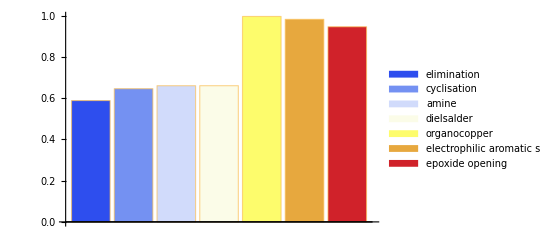

```mathematica
rclassBar=BarChart[Values[barDat][[{1,2,3,4,-1,-2,-3}]],ChartStyle->"TemperatureMap",ChartLegends->Keys@barDat[[{1,2,3,4,-1,-2,-3}]]]
```

```mathematica
Export["rclassBar.pdf",rclassBar]
```

rclassBar.pdf